#### Compute Dirac delta

```mathematica
u[t_,s_]:=(t+s+1)/2
v[t_,s_]:=(t-s+1)/2
calI[t_,s_]:=(288/24 (-5+s^2+t (2+t))^2)/((*x^2*) (1-s+t)^6 (1+s+t)^6) (π^2/4 (-5+s^2 +t (2+t))^2 UnitStep[t-(Sqrt[3]-1)]+(-(1-s+t)  (1+s+t) +1/2 (-5+s^2+t (2+t)) Log[Abs[(-2+t (2+t))/(3-s^2)]])^2)
funk[t_,s_]:=2((t(2+t)(s^2-1))/((1-s+t)(1+s+t)))^2 ;
redux=1/4; (*1*)
ClearAll[IQtsDirac];
IQtsDirac[k_,ks_,A_]:=Block[{ηv=400/k,s=0,t=-1+(2 ks)/k,dimplot=300,prefac,Kernel},
prefac=Ωr0h2 ((aF[ηv]HF[ηv])/(aF[ηout]HF[ηout]))^2 1/24(k/HF[ηv])^2;
Kernel=ComputeIQN[k,k u[t,s],k v[t,s],1] ;

(prefac 2  A^2 Kernel 1/k^2 funk[t,s])
]
```

```mathematica
AbsoluteTiming[test=ParallelTable[{k,IQtsDirac[k,10^2,1]},{k,10^Range[-1,2.3,3.3/(5 11-1)]}];]
```

{15.0567,Null}

```mathematica
With[{A=1,ks=10^2},
tabref=ParallelTable[{k,Ωr0h2 (*((aF[1/k]HF[1/k])/(aF[ηout]HF[ηout]))^2*)A^2 1/k^2(calI[t,s]funk[t,s]/.{s->0,t->-1+(2 ks)/k})},{k,10^Range[-1.,2.3,.005]}];
]
```

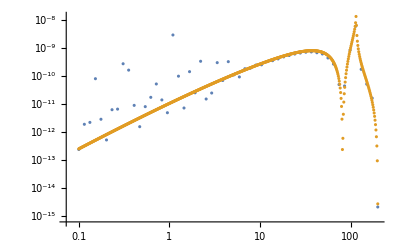

```mathematica
Show[ListLogLogPlot[{test,tabref}](*,LogLogPlot[10^-10. f^2.,{f,0.0001,100}]*)]
```

```mathematica
AbsoluteTiming[test=ParallelTable[{k,IQtsDirac[k,9.5,1]},{k,10^Range[-2+1,0.26+1,2.26/(4 11-1)]}];]
```

{138.145,Null}

```mathematica
With[{A=1,ks=9.5},
tabref=ParallelTable[{k,Ωr0h2 ((aF[1/k]HF[1/k])/(aF[ηout]HF[ηout]))^2 A^2 1/k^2(calI[t,s]funk[t,s]/.{s->0,t->-1+(2 ks)/k})},{k,10^Range[-2+1,0.26+1,.005]}];
]
```

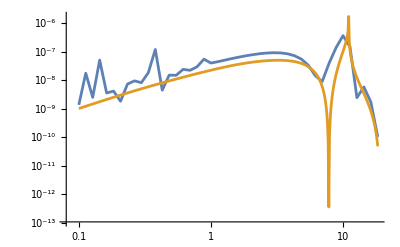

```mathematica
Show[ListLogLogPlot[{test,tabref},Joined->True]]
```

```mathematica
AbsoluteTiming[test=ParallelTable[{k,IQtsDirac[k,5 10^2,1]},{k,10^Range[-0.2,1.2,2.4/(4 11-1)]}];]
```

{81.7643,Null}

```mathematica
With[{A=1,ks=5 10^2},
tabref=ParallelTable[{k,Ωr0h2 ((aF[1/k]HF[1/k])/(aF[ηout]HF[ηout]))^2 A^2 1/k^2(calI[t,s]funk[t,s]/.{s->0,t->-1+(2 ks)/k})},{k,10^Range[-0.2,1.2,.005]}];
]
```

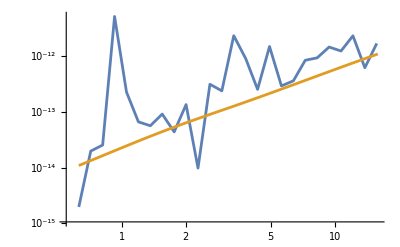

```mathematica
Show[ListLogLogPlot[{test,tabref},Joined->True]]
```